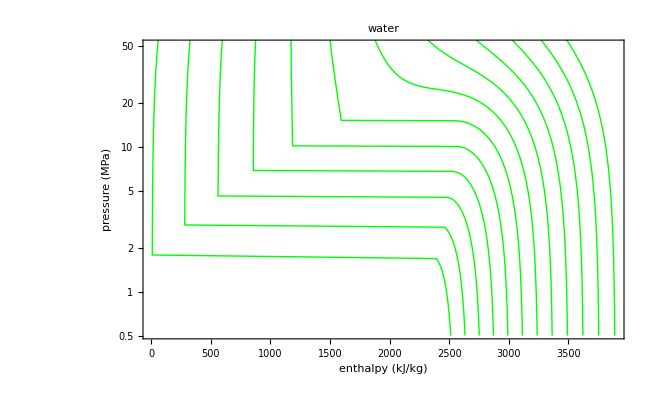

```mathematica
Module[{MW,R,Tref,Pref,Tc,Pc,CpA,CpB,CpC,CpD,Hig,Hdepref,ω,κ,A,B,a2,a1,a0,q,p,r,θ,Z,Hdep,H,p1,p2},

MW=18.02;(*kg/kmol*)
R=8.314/MW;(*kJ/kmol/K*)
Tref=298;Pref=0.1;
Tc=647.3;
Pc=22.12;

CpA=32.24;
CpB=0.001924;
CpC=1.055*10^-5;
CpD=-3.596*10^-9;
Hig=(CpA*(T-Tref)+1/2*CpB*(T^2-Tref^2)+1/3*CpC*(T^3-Tref^3)+1/4*CpD*(T^4-Tref^4))/MW;
Hdepref=-45729.2/MW;

ω=0.344;
κ=0.37464+1.54226*ω-0.26992*ω^2;

A=0.4572355289*(1+κ*(1-√(T/Tc)))^2*(Tc^2*P)/(T^2*Pc);
B=0.0777960739*(P*Tc)/(Pc*T);

(*ROOTS*)
a2=B-1;
a1=A-3*B^2-2*B;
a0=-A*B+B^2+B^3;

q=(2*a2^3-9*a2*a1+27*a0)/27;
p=(3*a1-a2^2)/3;

r=q^2/4+p^3/27;

θ=ArcCos[(3*q)/(2*p*√(-p/3))]/3;
Z=Piecewise[{{CubeRoot[-q/2+√r]+CubeRoot[-q/2-√r]-a2/3,r>0},{2*√(-p/3)*Cos[θ]-a2/3,r≤0}}];
Hdep=R*T*(Z-1-A/(2.8284*B)*(1+κ*√(T/(Tc*(1+κ*(1-√(T/Tc)))^2)))*Log[(Z+2.4142*B)/(Z-0.4142*B)]);
H=Table[Table[{Hdep-Hdepref+Hig,P},{P,0.5,55,0.1}],{T,300,1000,60}];


Show[
ListLogPlot[H,Joined->True,PlotStyle->{{Thick,Green}}],
Frame->True,FrameLabel->{Style["enthalpy (kJ/kg)",17],Style["pressure  (MPa)",17]},LabelStyle->{Black,14},
PlotRange->{Log@0.52,Log@50},Axes->False,ImageSize->650,PlotLabel->Style["water",18]]
]
```

```mathematica
list=Table[t,{t,80,300,20}]
list[[10]]
```

{80,100,120,140,160,180,200,220,240,260,280,300}

260